MixtureDistribution[{0.234069,0.765931},{GammaDistribution[0.391673,0.0441043],LogNormalDistribution[-1.54234,1.61588]}]

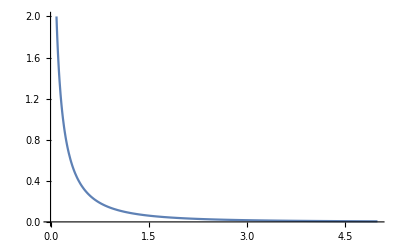

```mathematica
dist=FindDistribution[ScaledWidths]
Plot[PDF[dist,x],{x,0,5},PlotRange->{0,2}]
```

```mathematica
EstimatedDistribution[ScaledWidths,GenPTDistribution]
```

ProbabilityDistribution[(0.200571 ⅇ^(-0.257384 x))/x^0.742616,{x,0,∞}]

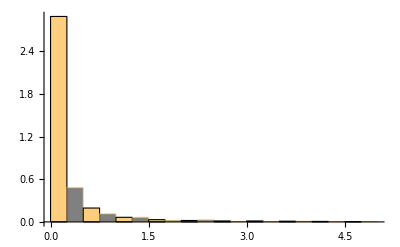

```mathematica
Histogram[ScaledWidths,{bins},"ProbabilityDensity",ChartStyle->{{EdgeForm[Black],Gray}}]
```

```mathematica
FindDistributionParameters[ScaledWidths,GenPTDistribution]
```

{ν→0.514768}

## Test of the nonlinear fit error

```mathematica
options1={Frame->True,LabelStyle->Large,GridLines->Automatic}
```

{Frame→True,LabelStyle→Large,GridLines→Automatic}

First let’s assume that there is a set of (x_i,y_i) data points,  Let’s define them and then plot them.

```mathematica
data= {{0, 1}, {1, 0}, {3, 2}, {5, 4}, {6, 4}, {7, 5}};
```

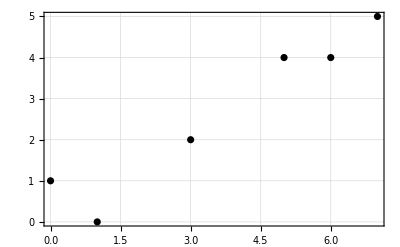

```mathematica
ListPlot[data,options1,PlotStyle->{Black}]
```

Now we’ll propose a function to fit to them with a free parameter a:

```mathematica
py[a_,x_]:=Exp[a x]
```

Do the fit

```mathematica
nlm= NonlinearModelFit[data, py[a,x], {a},x];
```

Append the “estimated variance”

σ=1/(n-1)(∑_(i=1))^n(y_i-py(x_i))^2

```mathematica
√(1/(Length[data]-1)Sum[(data[[i,2]]-py[a/.nlm["BestFitParameters"],data[[i,1]]])^2,{i,1,Length[data]}])
```

0.666591

```mathematica
mle= Append[nlm["BestFitParameters"],σ->nlm["EstimatedVariance"]^0.5]
```

{a→0.235746,σ→0.666591}

```mathematica
nlm["CovarianceMatrix"]
```

{{0.000198259}}

```mathematica
nlm["ParameterErrors"]
```

{0.0140804}

Let’s assume that the observed data may be binned to a normal distribution about the expected values.  The residual values y_i-y(x_i) are treated as the random variable.  Because the log is a monotonically increasing function of its argument, the maximum of the normal distribution occurs at the same point as the maximum of its log.  Construct the log likelihood function for the normal distribution with the estimated variance computed above:

logL=(∑_(i=1))^n log(P (y_i-y(x_i)) )=(∑_(i=1))^n log( (ⅇ^(-((y_i-py(x_i)))^2/(2 σ^2)))/(√(2 π) σ))

```mathematica
FunctionExpand[Sum[Log[Exp[-(data[[i,2]]-py[a,data[[i,1]]])^2/(2 σ^2)]/(√(2π)σ)],{i,1,Length[data]}],{σ>0,a>0}]
```

-ⅇ^(2 a)/(2 σ^2)-((2-ⅇ^(3 a))^2)/(2 σ^2)-((4-ⅇ^(5 a))^2)/(2 σ^2)-((4-ⅇ^(6 a))^2)/(2 σ^2)-((5-ⅇ^(7 a))^2)/(2 σ^2)+1/2 (-Log[2]-Log[π])+5 (-1/2 Log[2 π]-Log[σ])-Log[σ]

There is a built-in command for this.

```mathematica
logL=LogLikelihood[NormalDistribution[0,σ],data[[All,2]]-py[a,data[[All,1]]]]
```

-(ⅇ^(2 a)+(2-ⅇ^(3 a))^2+(4-ⅇ^(5 a))^2+(4-ⅇ^(6 a))^2+(5-ⅇ^(7 a))^2)/(2 σ^2)-6 (1/2 (Log[2]+Log[π])+Log[σ])

Then search for the values of a and σ that maximize this log-likelihood function

```mathematica
sol=NMaximize[{logL,σ>0&&a>0},{a,σ}]
```

{-5.53319,{a→0.235746,σ→0.608511}}

Let’s look at the graph to see the maximum:

```mathematica
Plot3D[logL,{a,.22,.25},{σ,0.5,0.7}]
```

-Graphics3D-

First define n to be the number of data points, and p to be the number of parameters.

```mathematica
n=Length[data];
p=1;
```

Adjust estimate of σ so that the estimator of σ^2 is “unbiased”.

```mathematica
sigma=σ Sqrt[n/(n-p)]/.sol[[2]]
```

0.666591

Modify the maximum likelihood estimate for σ

```mathematica
sol[[2,2]]=σ->sigma
```

σ→0.666591

Now get the standard errors for the estimators of a and b

First construct the second derivative of logL symbolically

This is just as before, but with x_i,y_i symbolically represented.

```mathematica
Clear[y]
```

```mathematica
symbolicData=Table[{x[i],y[i]},{i,n}];logL=LogLikelihood[NormalDistribution[0,σ],symbolicData[[All,2]]-py[a,symbolicData[[All,1]]]]
```

-6 (1/2 (Log[2]+Log[π])+Log[σ])-((-ⅇ^(a x[1])+y[1])^2+(-ⅇ^(a x[2])+y[2])^2+(-ⅇ^(a x[3])+y[3])^2+(-ⅇ^(a x[4])+y[4])^2+(-ⅇ^(a x[5])+y[5])^2+(-ⅇ^(a x[6])+y[6])^2)/(2 σ^2)

Take the second derivative of logL with respect to the free parameter a.

h=ⅆ^2/(ⅆ a^2)(∑_(i=1))^n log( (ⅇ^(-((y_i-py(a, x_i)))^2/(2 σ^2)))/(√(2 π) σ))

```mathematica
h=D[logL,{{a},2}]
```

{{-1/(2 σ^2)(2 ⅇ^(2 a x[1]) x[1]^2+2 ⅇ^(2 a x[2]) x[2]^2+2 ⅇ^(2 a x[3]) x[3]^2+2 ⅇ^(2 a x[4]) x[4]^2+2 ⅇ^(2 a x[5]) x[5]^2+2 ⅇ^(2 a x[6]) x[6]^2-2 ⅇ^(a x[1]) x[1]^2 (-ⅇ^(a x[1])+y[1])-2 ⅇ^(a x[2]) x[2]^2 (-ⅇ^(a x[2])+y[2])-2 ⅇ^(a x[3]) x[3]^2 (-ⅇ^(a x[3])+y[3])-2 ⅇ^(a x[4]) x[4]^2 (-ⅇ^(a x[4])+y[4])-2 ⅇ^(a x[5]) x[5]^2 (-ⅇ^(a x[5])+y[5])-2 ⅇ^(a x[6]) x[6]^2 (-ⅇ^(a x[6])+y[6]))}}

Now evaluate h at the data points

```mathematica
Eh=h/.y[i_]->py[a,x[i]]/.Table[x[i]->data[[i,1]],{i,n}]
```

{{-(2 ⅇ^(2 a)+18 ⅇ^(6 a)+50 ⅇ^(10 a)+72 ⅇ^(12 a)+98 ⅇ^(14 a))/(2 σ^2)}}

Take the minus the inverse and plug in the maximum likelihood estimators to get the estimates of the variances and covariance of the parameter estimators

```mathematica
cov=-Inverse[Eh]/.sol[[2]]
```

{{0.000198259}}

```mathematica
MatrixForm[cov]
```

(0.000198259)

Standard error for the estimator of a

```mathematica
cov[[1,1]]^0.5
```

0.0140804

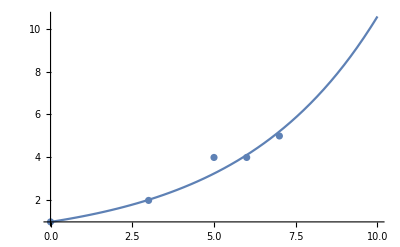

```mathematica
Show[Plot[py[a/.nlm["BestFitParameters"],x],{x,0,10}],ListPlot[data]]
```